```mathematica
Costo[t_]:=9.99-0.79Floor[-(t-1)]
```

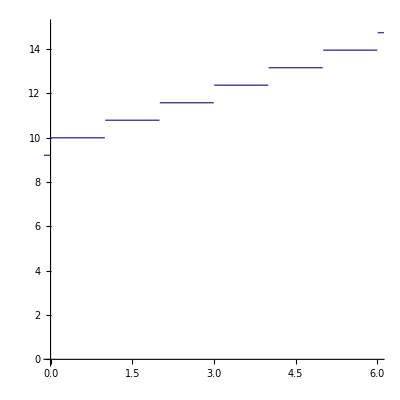

```mathematica
Plot[Costo[t],{t,-10,10},PlotRange->{{0,6},{0,15}}, AspectRatio->1]
```

```mathematica
Grid[Table[{t,N[Costo[t],5]},{t,3,4.1,0.1}], Frame->All]
```

3. | 11.57
3.1 | 12.36
3.2 | 12.36
3.3 | 12.36
3.4 | 12.36
3.5 | 12.36
3.6 | 12.36
3.7 | 12.36
3.8 | 12.36
3.9 | 12.36
4. | 12.36
4.1 | 13.15

```mathematica
Limit[Costo[t],t->3.5]
```

12.36

```mathematica
Limit[Costo[t],t->3,Direction->1]
```

11.57

```mathematica
Limit[Costo[t],t->3,Direction->-1]
```

12.36

```mathematica
(*El límite no existe en t=3 porque tiende a 11.57 por la izquierda y a 12.36 por la derecha*)
```

```mathematica
f1[x_]:=Expand[(Sqrt[x+5]-3)/(x-4)]   (*El dominio es [-5, +INF)-{4} *)
```

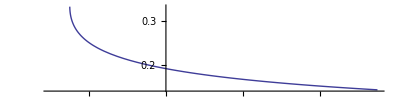

```mathematica
Plot[f1[x],{x,-6,11}, AspectRatio->1/4]
```

```mathematica
(*Por la forma de la gráfica se puede pensar que la función es lineal de -5 al infinito positivo, pero no es así porque la función no está definida en el punto x=4, el hueco en ese punto no se ve. Por eso es importante analizar de forma analítica la función y no guiarse sólo por la gráfica, la gráfica es sólo una referencia pero no muestra las discontinuidades*)


f2[x_]:=Expand[2x+1]

Manipulate[{Plot[f2[x],{x,1-a,1+a},PlotRange->{{-2,5},{-2,6}}],Abs[f2[a+1]-3],N[Abs[f2[1-a]-3]]},{a,0.0001,1,0.0001}]
```

```mathematica
Manipulate[{Plot[f2[x],{x,1-a,1+a},PlotRange->{{-2,5},{-2,6}}],Abs[f2[a+1]-3],N[Abs[f2[1-a]-3]]},{a,0.1,1,0.1}]
```

```mathematica
Manipulate[{Plot[f2[x],{x,1-a,1+a},PlotRange->{{-2,5},{-2,6}}],Abs[f2[a+1]-3],N[Abs[f2[1-a]-3]]},{a,0.5,1,0.5}]
```

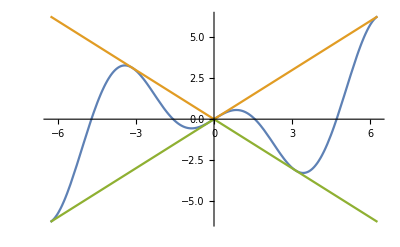

Plot::nonopt: Options expected (instead of {x, -0.1, 0.1}) beyond position 3 in Plot[f3[x], f4[x], {x, -0.1, 0.1}]. An option must be a rule or a list of rules.

```mathematica
f3[x_]:=Expand[x Cos[x]];
f4[x_]:=Expand[Abs[x]*Sin[x]];
f5[x_]:=Abs[x Sin[x]]
f6[x_]:=x Sin [1/x]
f7[x_]:=Abs[x]Cos[x]
f8[x_]:=x Cos [1/x]

Plot[{f3[x],Abs[x],-Abs[x]},{x,-2 Pi,2 Pi}]
```

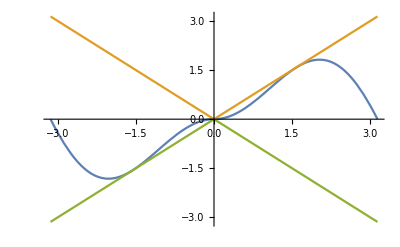

```mathematica
Plot[{f4[x],Abs[x],-Abs[x]},{x,-Pi,Pi}]
```

```mathematica
Plot[{f5[x],Abs[x],-Abs[x]},{x,-4,4}]
```

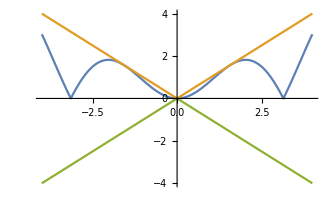

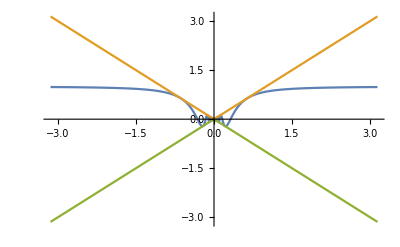

```mathematica
Plot[{f6[x],Abs[x],-Abs[x]},{x,-Pi,Pi}]
```

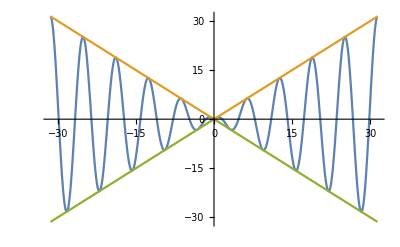

```mathematica
Plot[{f7[x],Abs[x],-Abs[x]},{x,-10Pi,10Pi}]
```

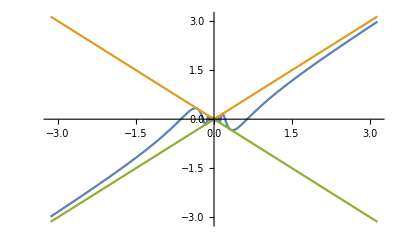

```mathematica
Plot[{f8[x],Abs[x],-Abs[x]},{x,-Pi,Pi}]
```

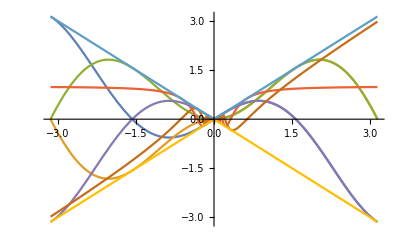

```mathematica
(*Ahora pondre todas las funciones en una misma grafica*)
Plot[{f3[x],f4[x],f5[x],f6[x],f7[x],f8[x],Abs[x],-Abs[x]},{x,-Pi,Pi}]
```

```mathematica
Limit[f3[x],x->0]
```

0

```mathematica
Limit[f4[x],x->0]
```

0

```mathematica
Limit[f5[x],x->0]
```

0

```mathematica
Limit[f6[x],x->0]
```

0

```mathematica
Limit[f7[x],x->0]
```

0

```mathematica
Limit[f8[x],x->0]
```

0

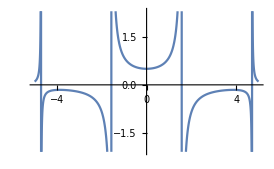
```mathematica
f9[x_]:=Expand[(Sec[x]-1)/(x^2)] (*El dominio de la funcion son todos los numeros reales menos el 0 porque el denominador x^2 y x=n(pi/2) siendo n un entero impar*)
Plot[f9[x],{x,-5,5}]
-Graphics-

(*A mi me parece evidente el dominio porque se que la grafica se corre una unidad a la derecha y porque la funcion Sec se vuelve indeterminada cunado x es igual a pi/2 o 3pi/2 por ejemplo, ya que la funcion coseno se vuelve cero en esos puntos y aunque no se vea en la funcion, el inverso multiplicativo del coseno es igual a la funcion secante*)

Limit[f9[x],x->0]
```

```mathematica
1/2

Limit[f9[x],x->0,Direction->1]
```

1/2

```mathematica
Limit[f9[x],x->0,Direction->-1]
```

1/2

```mathematica
(*El limite existe porque tiende a 1/2 por la izquierda, y a 1/2 por la derecha respectivamente*)
```

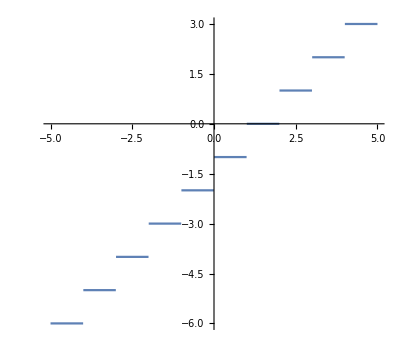

```mathematica
f10[x_]:=Expand[Floor[x]-1]
Plot[f10[x],{x,-5,5},AspectRatio->Automatic]
```

```mathematica
(*Evaluare los limites en un punto para ver el tipo de discontinuidad*)

Limit[f10[x],x->1,Direction->1]
```

-1

```mathematica
Limit[f10[x],x->1,Direction->-1]
```

0

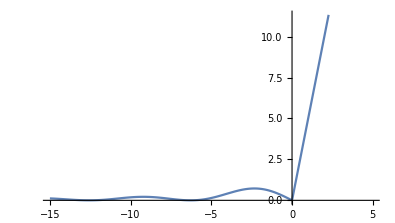

```mathematica
(*La discontinuidad es de tipo escencial con salto finito... tiende a -1 por la izquierda y a 0 por la derecha*)





f11[x_]:=Piecewise[{{((Cos[x]-1)/x),-Infinity<x<0},{5x,0≤x<Infinity}}]
Plot[f11[x], {x,-15,5}, AspectRatio->Automatic]
```

```mathematica
Limit[f11[x],x->0,Direction->1]
```

0

```mathematica
Limit[f11[x],x->0,Direction->-1]
```

0

```mathematica
(*El limite tanto por la derecha como por la izquierda coincide asi que el limite existe para x que tiende a 0, sin embargo la funcion tambien esta definida para x=0... asi que no hay discontinuidad en x=0 *)
```

```mathematica
f11[0]
```

0